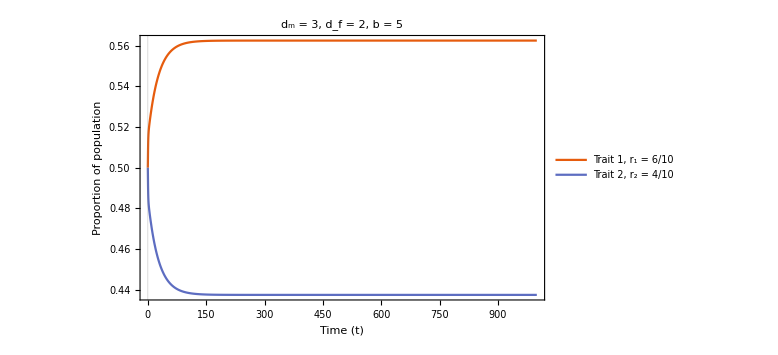

PresDR1.png

PresDR2.png

```mathematica
es1:=  -(1/2) b (Subscript[r, 1] (-1+Subscript[x, 1][t]) Subscript[y, 1][t]+Subscript[r, 2] Subscript[x, 1] [t]Subscript[y, 2][t]);
es2 := (1/2) (Subscript[y, 1][t] (2 Subscript[d, 1]-2 Subscript[d, 2]+b (1+Subscript[x, 1][t]-Subscript[r, 1] (1+Subscript[x, 1][t]+2 Subscript[y, 1][t])))+b (-(-1+Subscript[r, 2]) Subscript[x, 1][t]-2 Subscript[r, 2] Subscript[y, 1][t]) Subscript[y, 2][t]) ;
es3:= (1/2) (b Subscript[y, 1] [t]((-1+Subscript[r, 1]) (-1+Subscript[x, 1][t])-2 Subscript[r, 1] Subscript[y, 2][t])+Subscript[y, 2][t] (2 Subscript[d, 1]-2 Subscript[d, 2]+b (-1+Subscript[r, 2]) (-2+Subscript[x, 1][t])-2 b Subscript[r, 2] Subscript[y, 2][t]));

b = 5;
Subscript[r, 1] = 0.5;
Subscript[r, 2] =1;
Subscript[d, 1] = 2;
Subscript[d, 2] = 3;
tmax = 3*10^2;

sol = NDSolve[{Subscript[x, 1]'[t] == es1,Subscript[y, 1]'[t] == es2,Subscript[y, 2]'[t] == es3,Subscript[x, 1][0] == 0.5,Subscript[y, 1][0] == 1,Subscript[y, 2][0]== 1},{Subscript[x, 1],Subscript[y, 1],Subscript[y, 2]},{t,0,tmax}];

im1 =Plot[Evaluate[{(Subscript[x, 1][t] + Subscript[y, 1][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol,((1-Subscript[x, 1][t] )+ Subscript[y, 2][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol }],{t,0,tmax},PlotTheme -> "Scientific",FrameLabel -> {Style["Time (t)",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16],Style["Proportion of population",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16]},FrameTicksStyle -> Black,ImageSize -> Large,PlotLegends -> LineLegend[{Style["Trait 1, r_1 = 1/2",FontSize -> 16],Style["Trait 2, r_2 = 1",FontSize -> 16]},LabelStyle -> {"Black"}],FrameStyle->Directive[Black,FontSize->16],PlotLabel -> Style["d_m = 2, d_f = 3, b = 5",FontColor -> Black, FontSize -> 18]];

es1:=  -(1/2) b (Subscript[r, 1] (-1+Subscript[x, 1][t]) Subscript[y, 1][t]+Subscript[r, 2] Subscript[x, 1] [t]Subscript[y, 2][t]);
es2 := (1/2) (Subscript[y, 1][t] (2 Subscript[d, 1]-2 Subscript[d, 2]+b (1+Subscript[x, 1][t]-Subscript[r, 1] (1+Subscript[x, 1][t]+2 Subscript[y, 1][t])))+b (-(-1+Subscript[r, 2]) Subscript[x, 1][t]-2 Subscript[r, 2] Subscript[y, 1][t]) Subscript[y, 2][t]) ;
es3:= (1/2) (b Subscript[y, 1] [t]((-1+Subscript[r, 1]) (-1+Subscript[x, 1][t])-2 Subscript[r, 1] Subscript[y, 2][t])+Subscript[y, 2][t] (2 Subscript[d, 1]-2 Subscript[d, 2]+b (-1+Subscript[r, 2]) (-2+Subscript[x, 1][t])-2 b Subscript[r, 2] Subscript[y, 2][t]));

b = 5;
Subscript[r, 1] = 0.5;
Subscript[r, 2] =1;
Subscript[d, 1] = 3;
Subscript[d, 2] = 2;
tmax = 2*10^2;

sol2 = NDSolve[{Subscript[x, 1]'[t] == es1,Subscript[y, 1]'[t] == es2,Subscript[y, 2]'[t] == es3,Subscript[x, 1][0] == 0.5,Subscript[y, 1][0] == 1,Subscript[y, 2][0]== 1},{Subscript[x, 1],Subscript[y, 1],Subscript[y, 2]},{t,0,tmax}];

im2 =Plot[Evaluate[{(Subscript[x, 1][t] + Subscript[y, 1][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol2,((1-Subscript[x, 1][t] )+ Subscript[y, 2][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol2 }],{t,0,tmax},PlotTheme -> "Scientific",FrameLabel -> {Style["Time (t)",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16],Style["Proportion of population",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16]},FrameTicksStyle -> Black,ImageSize -> Large,PlotLegends -> LineLegend[{Style["Trait 1, r_1 = 1/2",FontSize -> 16],Style["Trait 2, r_2 = 1",FontSize -> 16]},LabelStyle -> {"Black"}],FrameStyle->Directive[Black,FontSize->16],PlotLabel -> Style["d_m = 3, d_f = 2, b = 5",FontColor -> Black, FontSize -> 18]];

b = 5;
Subscript[r, 1] = 0.6;
Subscript[r, 2] =0.4;
Subscript[d, 1] = 2;
Subscript[d, 2] = 3;
tmax = 10^3;

sol2 = NDSolve[{Subscript[x, 1]'[t] == es1,Subscript[y, 1]'[t] == es2,Subscript[y, 2]'[t] == es3,Subscript[x, 1][0] == 0.5,Subscript[y, 1][0] == 1,Subscript[y, 2][0]== 1},{Subscript[x, 1],Subscript[y, 1],Subscript[y, 2]},{t,0,tmax}];

im3 =Plot[Evaluate[{(Subscript[x, 1][t] + Subscript[y, 1][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol2,((1-Subscript[x, 1][t] )+ Subscript[y, 2][t])/(1 + Subscript[y, 1][t] + Subscript[y, 2][t]) /. sol2 }],{t,0,tmax},PlotTheme -> "Scientific",FrameLabel -> {Style["Time (t)",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16],Style["Proportion of population",FontColor -> Black, FontFamily -> "ComputerModern",FontSize -> 16]},FrameTicksStyle -> Black,ImageSize -> Large,PlotLegends -> LineLegend[{Style["Trait 1, r_1 = 6/10",FontSize -> 16],Style["Trait 2, r_2 = 4/10",FontSize -> 16]},LabelStyle -> {"Black"}],FrameStyle->Directive[Black,FontSize->16],PlotLabel -> Style["d_m = 3, d_f = 2, b = 5",FontColor -> Black, FontSize -> 18]];

Export["DR3.png",im3];
im3


Export["PresDR1.png",im1]
Export["PresDR2.png",im2]

c = GraphicsColumn[{im1,im2},ImageSize -> {875,850},Spacings->-50, Frame -> None];

Export["DRIm.png",c];
```